# Motor Physics, with Gears

Robert Atkinson, Maddy Nguyen, Samantha Hordyk, Cole Welch, and John Fraser
7 August 2018

An exploration of the physics of motors, in both symbolic and numeric form. A basic but sufficiently-complete parameterized model of a motor is presented. The differential equations governing that model are exhibited, and, from those, the (frequency domain) transfer functions of each of the model’s variables is developed from first principles. Next, mathematical infrastructure for converting the response of general frequency domain functions input signals is developed, then applied to the transfer functions as a function of the applied-voltage and external-applied-torque inputs. This yields time domain functions for each of the model’s variables in terms of the (symbolic) value of the model’s variables. With those time domain symbolic functions in hand, the steady-state response of the motor as a function of each of the model’s parameters is explored.

## Section. Administrivia

We begin by loading some handy utilities.

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
```

```mathematica
outputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGears.Output"}] <> $PathnameSeparator
CreateDirectory[outputDirectory] // Quiet;
```

C:\ftc\RobotPhysics\MotorPhysicsGears.Output\

## Section. Motor Model

The following figure gives a conceptual overview of a DC motor (ref: http://www.egr.msu.edu/classes/me451/jchoi/2008/).

-Graphics-

In addition to the the above, we also here incorporate into our model:

an (optional) Ν:1 reducing gearbox with associated efficiency

an autonomous time-dependent external torque

The state of the system can thus be described by the following variables.

vapp(t), the applied voltage (illustrated as ea(t) above)

i(t), the armature current

vg(t), the back EMF (‘g’ for ‘generator’; illustrated as eb(t) above)

θ(t), the angular position of the shaft, before the gearbox

ω(t), the angular velocity of the shaft, before the gearbox

α(t), the angular acceleration of the shaft, before the gearbox

τ(t), the torque driven by the armature current, before the gearbox

τappafter(t), an autonomous externally applied torque, after the gearbox. Often, this is constant, and caused by gravitational action.

The parameter constants that characterize the electrical aspects of the system are the following

Ke, the electromotive force constant

Kt, the motor torque constant

L, electric inductance

R, electric resistance

The following parameter constants characterize the mechanical aspects of the system

J, the moment of inertia of the armature etc before the gearbox

Jafter, the moment of inertia of any load or torque attached after the gearbox. May be (net) negative, depending on system; see τAfterExpr below.

B, motor viscous drag constant

Bafter, viscous drag of any load attached after the gearbox

η, the efficiency of the motor’s gear box (our current model does not support direction-dependent gearbox efficiencies).

Ν (capital nu), the reduction ratio of the gear box

We collect together basic information about our parameters.

```mathematica
parameterNames = {J, Jafter, B, Bafter, Ke, Kt, R, L, η,Ν}
parameterAssumptions = {};
parameterAssumptions = Union[parameterAssumptions, # ≥ 0& /@ {J, B, t}]; (*allow J & B to be zero so we can explore simpler motor models*)
parameterAssumptions = Union[parameterAssumptions, # >0& /@ {R, L, Ke,Kt,Ν, η}];
parameterAssumptions = Union[parameterAssumptions, # ∈Reals &/@{Jafter, Bafter, constvapp, constτappafter}];
parameterAssumptions = Union[parameterAssumptions, #[_] ∈ Reals & /@ {vapp, i, vg, θ, ω, α, τ,τappafter }]
```

{J,Jafter,B,Bafter,Ke,Kt,R,L,η,Ν}

{Bafter∈ℝ,constvapp∈ℝ,constτappafter∈ℝ,Jafter∈ℝ,i[_]∈ℝ,vapp[_]∈ℝ,vg[_]∈ℝ,α[_]∈ℝ,θ[_]∈ℝ,τ[_]∈ℝ,τappafter[_]∈ℝ,ω[_]∈ℝ,Ke>0,Kt>0,L>0,R>0,η>0,Ν>0,B≥0,J≥0,t≥0}

## Section. Differential Equations

### Section.Subsection. Differential Equation Development

#### Section.Subsection.Subsubsection. On Gearboxes and Torques

Our modelled system contains a gearbox with (reducing) gear ratio Ν and efficiency η. On either side of the gearbox we may have loads, drags, and driving torques, the latter being electrically generated on one side and externally applied on the other. In order to be able to write the torque differential equation for the system as a whole, we need to be able to take these two sets of torques as they are found in their respective separate places in the system and rewrite them both as the are effectively felt at some one point in the system. Commonly, in mechanical engineering this one point is chosen to be just before the gearbox, and the loads / torques after the gearbox are said to be “reflected” to create corresponding equivalent reflected loads and torques at the before-gearbox location.  Here, we develop the mathematics of carrying out this reflection.

Just a couple of principles are involved:

State related to angular position (position, velocity, acceleration, etc.) on the output side is 1 / Νth that of on the input side.

Torque on the output side is Ν η times that of on the input side.

```mathematica
Clear[reflectAngle, reflectTorque]
reflectAngle[expr_, out_, in_, t_] := expr /. {out[t] -> in[t] / Ν, Derivative[n_][out][t] :> Derivative[n][in][t] / Ν}
reflectAngle[expr_] := reflectAngle[expr, θafter, θ, t]
reflectTorque[τout_] := τout / (Ν η)

reflectTorque[constτappafter +Jafter θafter''[t] + Bafter θafter'[t]]// Expand
% // reflectAngle
```

constτappafter/(η Ν)+(Bafter θafter'[t])/(η Ν)+(Jafter θafter''[t])/(η Ν)

constτappafter/(η Ν)+(Bafter θ'[t])/(η Ν^2)+(Jafter θ''[t])/(η Ν^2)

#### Section.Subsection.Subsubsection. Differential Equation System

With that understanding on how to reflect torques, we can now develop the differential equations that govern the system.

The motor torque is proportional to current.

```mathematica
ktEqn = τ[t] == Kt i[t]
```

τ[t]==Kt i[t]

The back EMF is proportional to velocity.

```mathematica
backEmfEqn = vg[t] == Ke θ'[t]
```

vg[t]==Ke θ'[t]

The after-gearbox angular position is a simple ratio of the before-gearbox position. This also applies to the velocity and acceleration.

```mathematica
θafterEqns = Derivative[#][θafter][t] == Derivative[#][θ][t] / Ν & /@ Range[0, 2]
```

{θafter[t]==θ[t]/Ν,θafter'[t]==θ'[t]/Ν,θafter''[t]==θ''[t]/Ν}

Before the gearbox, the electrically driven motor torque is reduced by viscous drag and the inertia of the motor.

```mathematica
τBeforeExpr = τ[t] + - B θ'[t]- J θ''[t]
```

τ[t]-B θ'[t]-J θ''[t]

After the gearbox, we have an autonomous, time-dependant externally applied torque, a viscous drag, and an internal load and/or an acceleration-dependent external torque.

```mathematica
τAfterExpr = τappafter[t] -Bafter θafter'[t]-Jafter θafter''[t]
```

τappafter[t]-Bafter θafter'[t]-Jafter θafter''[t]

As all the torque must be accounted for, the sum of the before torques and the reflected after torques must be zero.

```mathematica
τEqn = τBeforeExpr + (τAfterExpr // reflectTorque // reflectAngle) == 0;
τEqn =Collect[τEqn, {θ[t], θ'[t], θ''[t]}]
```

τ[t]+τappafter[t]/(η Ν)+(-B-Bafter/(η Ν^2)) θ'[t]+(-J-Jafter/(η Ν^2)) θ''[t]==0

The voltage drop across the resistance, induction and back EMF must equal the applied voltage (due to one of Kirchhoff’s laws).

```mathematica
voltageEqn = vapp[t] == R i[t] + L i'[t] + vg[t]
```

vapp[t]==R i[t]+vg[t]+L i'[t]

We put it all together.

```mathematica
diffEqns = {ktEqn, backEmfEqn, voltageEqn, τEqn} ~Join~ θafterEqns // FullSimplify;
diffEqns // prettyPrint
```

Kt i(t)==τ(t)
vg(t)==Ke θ'(t)
R i(t)+vg(t)+L i'(t)==vapp(t)
(η τ(t) Ν^2+τappafter(t) Ν-(B η Ν^2+Bafter) θ'(t)-(J η Ν^2+Jafter) θ''(t))/(η Ν)==0
θafter(t)==(θ(t))/Ν
θafter'(t)==(θ'(t))/Ν
θafter''(t)==(θ''(t))/Ν

### Section.Subsection. Initial Conditions

Some of the initial conditions we can intuit intellectually:

```mathematica
initialConditions = {
θ[0]==0,
i[0]==0, 
vg[0]==0,
vapp[0] == ν,
τappafter[0] == Τ
}
```

{θ[0]==0,i[0]==0,vg[0]==0,vapp[0]==ν,τappafter[0]==Τ}

Others we can solve for:

```mathematica
diffEqFunctionsOfTime = Reap[Scan[If[MatchQ[#, _[t]], Sow [#]]&, diffEqns, Infinity]][[2,1]] // Union
others = Complement[diffEqFunctionsOfTime /. t -> 0, initialConditions[[All,1]]] 
(eqnsSubsKnownInitial = diffEqns /. t -> 0 /. (initialConditions /. Equal -> Rule) /. UnitStep[τ[0] θ'[0]] -> 1);
(solvedInitialConditions =(uniqueSolve[eqnsSubsKnownInitial, others] /. Rule -> Equal));
(allInitialConditions = solvedInitialConditions ~Join~ initialConditions) // prettyPrint
```

{i[t],vapp[t],vg[t],θ[t],θafter[t],τ[t],τappafter[t],i'[t],θ'[t],θafter'[t],θ''[t],θafter''[t]}

{θafter[0],τ[0],i'[0],θ'[0],θafter'[0],θ''[0],θafter''[0]}

θafter(0)==0
τ(0)==0
i'(0)==ν/L
θ'(0)==0
θafter'(0)==0
θ''(0)==(Ν Τ)/(J η Ν^2+Jafter)
θafter''(0)==Τ/(J η Ν^2+Jafter)
θ(0)==0
i(0)==0
vg(0)==0
vapp(0)==ν
τappafter(0)==Τ

## Section. Motor Parameters

### Section.Subsection. Motor Parameter Units

We develop infrastructure regarding the units in which each of our parameters are specified. This will help us sanity check the structure of our equations, as they must be internally consistent in their use of units (e.g.: no velocities added to masses, etc).

A note on radians as a unit. The Bureau International des Poids et Mesures, the intergovernmental organization that standardizes the SI, officially refers to a radian as “a special name is given to the unit one, in order to facilitate the identification of the quantity involved” (Ref: https://www.bipm.org/en/publications/si-brochure/section2-2-3.html). With that as background, we have here chosen to include radians in all places in which they logically belong, as doing so provides valuable insight regarding the quantities being manipulated. Thus, for example, you will find here torque having units of N m / radian instead of N m, and the like. As, from the SI perspective, this amounts to multiplying or dividing by the unit one, no semantic change is effected.

Aside: in the opinion of one of the authors (Atkinson), that “a special name given to the unit one” is in any way at all different than a first-class “unit” is a perspective reasonable only if one artificially and myopically limits one’s worldview to contain only the seven units whose dimension is necessarily experimentally calibrated as opposed to units whose dimension is mathematically or otherwise calibrated, such as radian, becquerel, motor encoder ticks, etc. And the world is chock-full of the latter. But this is a discussion for another time. See also Jacques E. Romain,  “Angle as a Fourth Fundamental Quantity”, Journal of Research of the National Bureau of Standards-B. Mathematics and Mathematical Physics, Vol. 66B,  No. 3, July- September 1962.

```mathematica
radiansUnits = parseUnit["Radians"];
secondsUnits = parseUnit["Seconds"];
siAngularPositionUnits = radiansUnits;
siAngularVelocityUnits = siAngularPositionUnits / secondsUnits;
siAngularAccelerationUnits = siAngularVelocityUnits / secondsUnits;
siTorqueUnits = parseUnit["N m"] / radiansUnits;
siAngularViscousDragUnits = siTorqueUnits / siAngularVelocityUnits;
siAngularInertialUnits = siTorqueUnits / siAngularAccelerationUnits;

parameterUnits = {
R -> parseUnit["Ohms"],
L -> parseUnit["Henrys"],
i[t] -> parseUnit["Amperes"],
i'[t] -> parseUnit["Amperes"] / secondsUnits,
i''[t] -> parseUnit["Amperes"] / secondsUnits / secondsUnits,
vapp[t] -> parseUnit["Volts"],
constvapp -> parseUnit["Volts"],
vg[t] -> parseUnit["Volts"],

J -> siAngularInertialUnits,
Jafter -> siAngularInertialUnits,
B -> siAngularViscousDragUnits,
Bafter -> siAngularViscousDragUnits,

Ke -> parseUnit["Seconds Volts / Radians"], 
KeShaft -> parseUnit["Seconds Volts / Radians"], 

Kt -> parseUnit["Newtons Meters"] / parseUnit["Amperes"] / radiansUnits,
KtShaft -> parseUnit["Newtons Meters"] / parseUnit["Amperes"] / radiansUnits,

θ[t]-> siAngularPositionUnits,θafter[t] -> siAngularPositionUnits,
θ'[t]-> siAngularVelocityUnits,θafter'[t] -> siAngularPositionUnits,
θ''[t]-> siAngularAccelerationUnits,θafter''[t] -> siAngularPositionUnits,
ω[t]-> siAngularVelocityUnits,
α[t]-> siAngularAccelerationUnits,

τ[t] -> siTorqueUnits,
τappafter[t] -> siTorqueUnits,
constτappafter -> siTorqueUnits,

Ν -> parseUnit["DimensionlessUnit"],
η -> parseUnit["DimensionlessUnit"]
} // Association
unitsToQuantities[units_] := Module[{rules, makeQuantity},
rules = Normal[units];
makeQuantity = Function[{param, unit}, Quantity[param, unit]];
(#[[1]] -> makeQuantity @@ # &/@ rules) // Association
]
parameterQuantities = unitsToQuantities[parameterUnits]
```

<|R→Ohms,L→Henries,i[t]→Amperes,i'[t]→Amperes/Seconds,i''[t]→Amperes/Seconds^2,vapp[t]→Volts,constvapp→Volts,vg[t]→Volts,J→(Meters Newtons Seconds^2)/Radians^2,Jafter→(Meters Newtons Seconds^2)/Radians^2,B→(Meters Newtons Seconds)/Radians^2,Bafter→(Meters Newtons Seconds)/Radians^2,Ke→(Seconds Volts)/Radians,KeShaft→(Seconds Volts)/Radians,Kt→(Meters Newtons)/(Amperes Radians),KtShaft→(Meters Newtons)/(Amperes Radians),θ[t]→Radians,θafter[t]→Radians,θ'[t]→Radians/Seconds,θafter'[t]→Radians,θ''[t]→Radians/Seconds^2,θafter''[t]→Radians,ω[t]→Radians/Seconds,α[t]→Radians/Seconds^2,τ[t]→(Meters Newtons)/Radians,τappafter[t]→(Meters Newtons)/Radians,constτappafter→(Meters Newtons)/Radians,Ν→DimensionlessUnit,η→DimensionlessUnit|>

<|R→R Ω,L→L H,i[t]→i[t] A,i'[t]→i'[t] A/s,i''[t]→i''[t] A/s^2,vapp[t]→vapp[t] V,constvapp→constvapp V,vg[t]→vg[t] V,J→J m s^2 N/rad^2,Jafter→Jafter m s^2 N/rad^2,B→B m s N/rad^2,Bafter→Bafter m s N/rad^2,Ke→Ke s V/rad,KeShaft→KeShaft s V/rad,Kt→Kt m N/(A rad),KtShaft→KtShaft m N/(A rad),θ[t]→θ[t] rad,θafter[t]→θafter[t] rad,θ'[t]→θ'[t] rad/s,θafter'[t]→θafter'[t] rad,θ''[t]→θ''[t] rad/s^2,θafter''[t]→θafter''[t] rad,ω[t]→ω[t] rad/s,α[t]→α[t] rad/s^2,τ[t]→τ[t] m N/rad,τappafter[t]→τappafter[t] m N/rad,constτappafter→constτappafter m N/rad,Ν→Ν ,η→η |>

Let’s look and see if our units are consistent:

```mathematica
diffEqns /. parameterQuantities // ColumnForm
```

Kt i[t] m N/rad==τ[t] m N/rad
vg[t] V==Ke θ'[t] V
(R i[t]+vg[t]+L i'[t]) A Ω==vapp[t] V
(η Ν^2 τ[t]+Ν τappafter[t]-(Bafter+B η Ν^2) θ'[t]-(Jafter+J η Ν^2) θ''[t])/(η Ν) m N/rad==0
θafter[t] rad==θ[t]/Ν rad
θafter'[t] rad==θ'[t]/Ν rad/s
θafter''[t] rad==θ''[t]/Ν rad/s^2

Huzzah! They check out (if the units were incompatible, Mathematica would’ve told us).

We save information regarding our parameters for later use.

```mathematica
saveDefinitions[outputDirectory <> "ParametersUnitsAndAssumptions.m", {parameterUnits, parameterQuantities, parameterAssumptions, radiansUnits, secondsUnits, siAngularPositionUnits, siAngularVelocityUnits, siAngularAccelerationUnits, siTorqueUnits, siAngularViscousDragUnits, siAngularInertialUnits}]
```

### Section.Subsection. On Ke & Kt

A brief digression. It is often remarked that, in compatible units, Ke & Kt have the same magnitude and sign. However, while often true, this relation does not always hold.

Recall our differential equations:

```mathematica
diffEqns // ColumnForm
```

Kt i[t]==τ[t]
vg[t]==Ke θ'[t]
R i[t]+vg[t]+L i'[t]==vapp[t]
(η Ν^2 τ[t]+Ν τappafter[t]-(Bafter+B η Ν^2) θ'[t]-(Jafter+J η Ν^2) θ''[t])/(η Ν)==0
θafter[t]==θ[t]/Ν
θafter'[t]==θ'[t]/Ν
θafter''[t]==θ''[t]/Ν

In steady state, the current and speed are constant.

```mathematica
(ssEqns = diffEqns /. {i'[t] -> 0, θ''[t] -> 0}) // ColumnForm
(ssEqns = Eliminate[ssEqns, {vg[t], B, θafter[t],θafter'[t], θafter''[t],τappafter[t]}]) // ColumnForm
(ssEqns  = ssEqns[[1;;2]]) // ColumnForm
```

Kt i[t]==τ[t]
vg[t]==Ke θ'[t]
R i[t]+vg[t]==vapp[t]
(η Ν^2 τ[t]+Ν τappafter[t]-(Bafter+B η Ν^2) θ'[t])/(η Ν)==0
θafter[t]==θ[t]/Ν
θafter'[t]==θ'[t]/Ν
θafter''[t]==0

Kt i[t]==τ[t]
vapp[t]==R i[t]+Ke θ'[t]
η≠0
Ν≠0

Kt i[t]==τ[t]
vapp[t]==R i[t]+Ke θ'[t]

From a power point of view (ref: https://bit.ly/2Lxka0Z), we must have (electrical) power in = (mechanical) power out + (electrical + other) power losses:

```mathematica
powerEqns = And @@ {
pwrIn == vapp[t] i[t],
pwrOut == τ[t] θ'[t],
pwrLosses == i[t]^2 R + pwrOtherPowerLosses,
pwrIn == pwrOut + pwrLosses
};
(ssPowerEqns = Union[ssEqns, powerEqns]) // prettyPrint
```

pwrIn==pwrLosses+pwrOut
pwrIn==i(t) vapp(t)
pwrLosses==R (i(t))^2+pwrOtherPowerLosses
pwrOut==τ(t) θ'(t)
Kt i(t)==τ(t)
vapp(t)==R i(t)+Ke θ'(t)

Let’s eliminate a few of the variables that we’re not interested in.

```mathematica
kBalanceEqns = Eliminate[ssPowerEqns, {i[t], τ[t], θ'[t], vapp[t]}];
kBalanceEqns // prettyPrint
uniqueSolve[kBalanceEqns[[2]], pwrOtherPowerLosses] /. Rule -> Equal
```

pwrIn==pwrLosses+pwrOut
Kt pwrOtherPowerLosses==(Ke-Kt) pwrOut

{pwrOtherPowerLosses==((Ke-Kt) pwrOut)/Kt}

We can conclude that if other power losses are zero, then Ke must equal Kt.

### Section.Subsection. Experimental Motor Data

We have experimental data from several motors (Nguyen, Hordyk, & Fraser, 2017). We load in same.

```mathematica
Clear[importMotorData, motorData]
importMotorData[] := importMotorData["Characterized Motors (Gears).xlsx"];
importMotorData[file_] := Module[{},
Import[NotebookDirectory[]<> file, {"Data", 1}][[2;; ]]
]
motorData = importMotorData[];
(motorData) // TableForm
```

Name | R | L (uH) | L (H) | Ke (>gear) | Kt (>gear, est) | Ke (<gear) | Kt (<gear, est) | J | b | N | ηf (est) | ηr (est)
AM 20 A | 2.3 | 691. | 0.000691 | 0.351 | 0.351 | 0.01755 | 0.01755 | 9.011×10^-6 | 0.0022 | 20. | 0.9 | 0.8
AM 20 B | 1.9 | 684. | 0.000684 | 0.389 | 0.389 | 0.01945 | 0.01945 | 9.011×10^-6 | 0.0025 | 20. | 0.9 | 0.8
AM 20 C | 5.1 | 717. | 0.000717 | 0.385 | 0.385 | 0.01925 | 0.01925 | 8.931×10^-6 | 0.0028 | 20. | 0.9 | 0.8
AM 40 A | 2.5 | 674. | 0.000674 | 0.753 | 0.753 | 0.018825 | 0.018825 | 0.00002221 | 0.2269 | 40. | 0.9 | 0.8
AM 40 B | 3.8 | 705. | 0.000705 | 0.705 | 0.705 | 0.017625 | 0.017625 | 0.00001741 | 0.56 | 40. | 0.9 | 0.8
AM 40 C | 2.1 | 716. | 0.000716 | 0.763 | 0.763 | 0.019075 | 0.019075 | 0.00002471 | 0.018 | 40. | 0.9 | 0.8
AM 60 A | 3.3 | 694. | 0.000694 | 1.066 | 1.066 | 0.0177667 | 0.0177667 | 0.00001041 | 0.033 | 60. | 0.9 | 0.8
AM 60 B | 5.1 | 696. | 0.000696 | 1.076 | 1.076 | 0.0179333 | 0.0179333 | 8.421×10^-6 | 0.02 | 60. | 0.9 | 0.8
AM 3.7 A | 8.9 | 679. | 0.000679 | 0.099 | 0.099 | 0.0267568 | 0.0267568 | 0.00002791 | 0.00014 | 3.7 | 0.9 | 0.8
AM 3.7 B | 2.6 | 797. | 0.000797 | 0.108 | 0.108 | 0.0291892 | 0.0291892 | 0.00003151 | 0.000176 | 3.7 | 0.9 | 0.8
AM 3.7 C | 8.7 | 880. | 0.00088 | 0.105 | 0.105 | 0.0283784 | 0.0283784 | 0.00003091 | 0.00017 | 3.7 | 0.9 | 0.8
Matrix A | 3.8 | 718. | 0.000718 | 0.34 | 0.34 | 0.00643939 | 0.00643939 | 9.431×10^-6 | 0.00151 | 52.8 | 0.9 | 0.8
Matrix B | 7.8 | 777. | 0.000777 | 0.363 | 0.363 | 0.006875 | 0.006875 | 7.761×10^-6 | 0.00191 | 52.8 | 0.9 | 0.8
Matrix C | 20.6 | 658. | 0.000658 | 0.338 | 0.338 | 0.00640152 | 0.00640152 | 7.231×10^-6 | 0.00186 | 52.8 | 0.9 | 0.8
CoreHex A | 3.6 | 1356. | 0.001356 | 0.822 | 0.822 | 0.0226759 | 0.0226759 | 0.0007331 | 0.0112 | 36.25 | 0.9 | 0.8
CoreHex B | 11.3 | 1352. | 0.001352 | 0.858 | 0.858 | 0.023669 | 0.023669 | 0.0006551 | 0.008 | 36.25 | 0.9 | 0.8
CoreHex C | 5.6 | 1342. | 0.001342 | 0.711 | 0.711 | 0.0196138 | 0.0196138 | 0.0004541 | 0.0078 | 36.25 | 0.9 | 0.8

We build a function to retrieve data from the table. We convert from floating point to rational in order to help delay floating point collapse later on down the line. We include load and external torque parameters at zero level so these can be easily added to later.

```mathematica
Clear[motorParameters]; 
Options[motorParameters] = { Geared -> True , Efficiency -> "Forward" };
validateOption[motorParameters][Geared, val_]  := BooleanQ[val];
validateOption[motorParameters][Efficiency, val_]  := MemberQ[{"Forward", "Reverse"}, val];

motorParameters[motorName_, opts: OptionsPattern[]] := motorParameters[motorData, motorName, opts]
motorParameters[motorData_, motorName_, opts: OptionsPattern[]] := validateOptions[]@ Module[{row, paramValues, quantify, qty, assoc},
row = Select[motorData, #[[1]] == motorName&][[1]];
paramValues =#[[1]] -> toRational[ row[[#[[2]]]] ]&/@ {
{R, 2}, {L, 4}, {KeShaft, 5}, {KtShaft, 6}, {Ke, 7}, {Kt, 8},  {J, 9}, {B, 10},
{Ν, 11}, {η, If[OptionValue[Efficiency]== "Forward", 12, 13]} };
quantify = Function[{name, value}, 
qty = (name /. parameterQuantities);
name ->Quantity[value, QuantityUnit[qty]]
] ;
assoc = quantify @@ #&/@ paramValues // Association;
assoc[Jafter] = Quantity[0, siAngularInertialUnits];
assoc[Bafter] = Quantity[0, siAngularViscousDragUnits];
assoc[constτappafter] = Quantity[0, siTorqueUnits];
If[!OptionValue[Geared],
assoc[Ν] = 1; 
assoc[η] = 1;
assoc[Ke] = assoc[KeShaft];
assoc[Kt] = assoc[KtShaft];
];
(* remove the shaft values to avoid confusion *)
assoc[KeShaft] =.;
assoc[KtShaft] =.;
assoc // siUnits // simplifyUnits
];

motorParameters["AM 60 A", Geared -> False]
motorParameters["AM 60 A", Geared -> True, Efficiency -> "Reverse"]
```

<|R→33/10 W/A^2,L→347/500000 H,Ke→533/500 kg m^2/(s^2 A rad),Kt→533/500 kg m^2/(s^2 A rad),J→1041/100000000 kg m^2/rad^2,B→33/1000 kg m^2/(s rad^2),Ν→1,η→1,Jafter→0 kg m^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→0 kg m^2/(s^2 rad)|>

<|R→33/10 W/A^2,L→347/500000 H,Ke→533/30000 kg m^2/(s^2 A rad),Kt→533/30000 kg m^2/(s^2 A rad),J→1041/100000000 kg m^2/rad^2,B→33/1000 kg m^2/(s rad^2),Ν→60,η→4/5,Jafter→0 kg m^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→0 kg m^2/(s^2 rad)|>

### Section.Subsection. Loads on the Motor

motorLoad[] creates a motor load given explicit internal and drag parameters. We allow the ‘out’ suffix but do not require its use.

```mathematica
Clear[motorLoad]
Options[motorLoad] = {
J -> Quantity[0, siAngularInertialUnits], Jafter -> Quantity[0, siAngularInertialUnits],
B -> Quantity[0, siAngularViscousDragUnits], Bafter -> Quantity[0, siAngularViscousDragUnits],
constτappafter -> Quantity[0, siTorqueUnits]
};
motorLoad[opts: OptionsPattern[]] := Module[{assoc = Association[]},
assoc[Jafter] = OptionValue[J] + OptionValue[Jafter];
assoc[Bafter] = OptionValue[B] + OptionValue[Bafter];
assoc[constτappafter] = OptionValue[constτappafter];
assoc
]
```

flywheel[] creates a motor load given mass and radius parameters

```mathematica
Clear[flywheel]
flywheel[mass_, radius_] := motorLoad[J -> mass * radius ^2 / 2 / Quantity[1, "Radians^2"]]
flywheel[Quantity[2, "kg"], Quantity[5, "cm"]]
```

<|Jafter→25 kg cm^2/rad^2,Bafter→0 m s N/rad^2,constτappafter→0 m N/rad|>

addMotorLoad[] takes motor parameters and a load and returns new parameters that include the load.

```mathematica
addMotorLoad[motor_, load_] := Module[{assoc},
assoc = Association[motor]; (*explicitly create copy*)
assoc[Jafter] = (Jafter /. motor) + (Jafter /. load);
assoc[Bafter] = (Bafter /. motor) + (Bafter /. load);
assoc[constτappafter] = (constτappafter /. motor) + (constτappafter /. load);
assoc
]
addMotorLoad[motorParameters["AM 60 A"], flywheel[Quantity[2, "kg"], Quantity[5, "cm"]]]
```

<|R→33/10 W/A^2,L→347/500000 H,Ke→533/30000 kg m^2/(s^2 A rad),Kt→533/30000 kg m^2/(s^2 A rad),J→1041/100000000 kg m^2/rad^2,B→33/1000 kg m^2/(s rad^2),Ν→60,η→9/10,Jafter→25 kg cm^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→0 m N/rad|>

### Section.Subsection. Mass on pulley

Here, we model a mass suspended on a massless “rigid string” from a massless pulley attached to the motor shaft. That string acts at a wrench with a length of the radius of the pulley to deliver a torque to the shaft. τMassOnPulley[] computes that torque.

There is a force pulling down on the mass due to gravity and up due to acceleration in the string that results from the driven angular acceleration of the motor shaft. The sum of these forces is the tension in the string. If the net acceleration is negative (ie: downward), a real (flexible) string would clamp at zero and have the mass in free-fall; we choose not to model that for now. Instead, here, our hypothetical rigid string continues to impart acceleration from the pulley even for negative accelerations. This is a bit odd for a string, but more reasonable if the string were in fact a rigid arm being lifted, or some such.

```mathematica
Clear[massOnPulley]
massOnPulley[mass_, radius_] := Module[
{gravityAcceleration, gravityForce, angularAcceleration, tangentialAcceleration, tangentialForce, tension, torque, unit, parts,radians = Quantity["Radians"]},

(* gravity exerts a constant downard force by acting on the mass *)
gravityAcceleration = Quantity["StandardAccelerationOfGravity"];
gravityForce =  gravityAcceleration * mass;

(* angular accelearation, converted to tangential acceration also acts on the mass to create an upward force *)
angularAcceleration = Quantity[θ''[t], siAngularAccelerationUnits];
tangentialAcceleration = angularAcceleration * radius / radians;
tangentialForce = tangentialAcceleration * mass;

(* the net force (the tension in the string) is the sum of the two forces*)
tension = gravityForce + tangentialForce;

(* the tension acts like a wrench with lever arm 'radius' *)
torque = tension * radius / radians;

(* we decompose the torque into constant and acceleration-dependent parts for output *)
unit =  QuantityUnit[torque];
parts = List @@(QuantityMagnitude[torque] // Apart);
motorLoad[constτappafter -> Quantity[parts[[1]], unit], Jafter -> Quantity[parts[[2]], unit] / angularAcceleration]
]
massOnPulley[Quantity[weightLbs, "Pounds"], Quantity[rInches, "Inches"]]
% // siUnits // clearUnits // N
```

<|Jafter→rInches^2 weightLbs lb in^2/rad^2,Bafter→0 m s N/rad^2,constτappafter→(196133 rInches weightLbs)/508 lb in^2/(s^2 rad)|>

<|Jafter→0.00029264 rInches^2 weightLbs,Bafter→0.,constτappafter→0.112985 rInches weightLbs|>

### Section.Subsection. Example Motors

We define a motor and loads that we’ll use to illustrate examples. We also define a generic, abstract motor that can help explore things symbolically.

‘aMotorClassic’ is the configuration we explored in our previous work. Ref: https://github.com/rgatkinson/RobotPhysics/blob/master/MotorPhysics.pdf

```mathematica
aMotor = motorParameters["AM 60 A"] 
aMotorClassic = addMotorLoad[motorParameters["AM 60 A", Geared -> False] , motorLoad[J -> Quantity[1, siAngularInertialUnits]]]
aFlywheel = flywheel[Quantity[1, "kg"], Quantity[5, "cm"]] // siUnits
aPulley = massOnPulley[Quantity[3, "Pounds"], Quantity[2, "Inches"]] // siUnits
```

<|R→33/10 W/A^2,L→347/500000 H,Ke→533/30000 kg m^2/(s^2 A rad),Kt→533/30000 kg m^2/(s^2 A rad),J→1041/100000000 kg m^2/rad^2,B→33/1000 kg m^2/(s rad^2),Ν→60,η→9/10,Jafter→0 kg m^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→0 kg m^2/(s^2 rad)|>

<|R→33/10 W/A^2,L→347/500000 H,Ke→533/500 kg m^2/(s^2 A rad),Kt→533/500 kg m^2/(s^2 A rad),J→1041/100000000 kg m^2/rad^2,B→33/1000 kg m^2/(s rad^2),Ν→1,η→1,Jafter→1 kg m^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→0 m N/rad|>

<|Jafter→1/800 kg m^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→0 kg m^2/(s^2 rad)|>

<|Jafter→2194797400719/625000000000000 kg m^2/rad^2,Bafter→0 kg m^2/(s rad^2),constτappafter→3389544870828501/5000000000000000 kg m^2/(s^2 rad)|>

```mathematica
genericMotor = # -> (# /. parameterQuantities)& /@ Keys[aMotor]
genericMotorLoad = # -> (# /. parameterQuantities)& /@ Keys[aFlywheel]
```

{R→R Ω,L→L H,Ke→Ke s V/rad,Kt→Kt m N/(A rad),J→J m s^2 N/rad^2,B→B m s N/rad^2,Ν→Ν ,η→η ,Jafter→Jafter m s^2 N/rad^2,Bafter→Bafter m s N/rad^2,constτappafter→constτappafter m N/rad}

{Jafter→Jafter m s^2 N/rad^2,Bafter→Bafter m s N/rad^2,constτappafter→constτappafter m N/rad}

## Section. Laplace Transforms and Transfer Function Models

### Section.Subsection. Laplace Transforms

Returning to the differential equations, we form the Laplace Transform of each, then solve the for the various transforms. First, we apply the LaplaceTransform[] function to each equation. It automatically makes use of the linearity of the transform, and insinuates itself just around the time dependent parts (ie: the parts dependent on the time variable we told it about, namely t).

```mathematica
diffEqnsSimplified = FullSimplify[Eliminate[diffEqns, {η[t]}], parameterAssumptions];
leqns = LaplaceTransform[#, t, s] &/@ diffEqns
leqns // prettyPrint
```

{Kt LaplaceTransform[i[t],t,s]==LaplaceTransform[τ[t],t,s],LaplaceTransform[vg[t],t,s]==Ke (s LaplaceTransform[θ[t],t,s]-θ[0]),R LaplaceTransform[i[t],t,s]+L (-i[0]+s LaplaceTransform[i[t],t,s])+LaplaceTransform[vg[t],t,s]==LaplaceTransform[vapp[t],t,s],1/(η Ν)(η Ν^2 LaplaceTransform[τ[t],t,s]+Ν LaplaceTransform[τappafter[t],t,s]-(Bafter+B η Ν^2) (s LaplaceTransform[θ[t],t,s]-θ[0])-(Jafter+J η Ν^2) (s^2 LaplaceTransform[θ[t],t,s]-s θ[0]-θ'[0]))==0,LaplaceTransform[θafter[t],t,s]==LaplaceTransform[θ[t],t,s]/Ν,s LaplaceTransform[θafter[t],t,s]-θafter[0]==(s LaplaceTransform[θ[t],t,s]-θ[0])/Ν,s^2 LaplaceTransform[θafter[t],t,s]-s θafter[0]-θafter'[0]==(s^2 LaplaceTransform[θ[t],t,s]-s θ[0]-θ'[0])/Ν}

Kt (ℒ_t[i(t)](s))==ℒ_t[τ(t)](s)
ℒ_t[vg(t)](s)==Ke (s (ℒ_t[θ(t)](s))-θ(0))
R (ℒ_t[i(t)](s))+L (s (ℒ_t[i(t)](s))-i(0))+ℒ_t[vg(t)](s)==ℒ_t[vapp(t)](s)
(η (ℒ_t[τ(t)](s)) Ν^2+(ℒ_t[τappafter(t)](s)) Ν-(B η Ν^2+Bafter) (s (ℒ_t[θ(t)](s))-θ(0))-(J η Ν^2+Jafter) ((ℒ_t[θ(t)](s)) s^2-θ(0) s-θ'(0)))/(η Ν)==0
ℒ_t[θafter(t)](s)==(ℒ_t[θ(t)](s))/Ν
s (ℒ_t[θafter(t)](s))-θafter(0)==(s (ℒ_t[θ(t)](s))-θ(0))/Ν
(ℒ_t[θafter(t)](s)) s^2-θafter(0) s-θafter'(0)==((ℒ_t[θ(t)](s)) s^2-θ(0) s-θ'(0))/Ν

Next, we walk those equations, picking up those insinuations and sowing them to the wind, reaping them on the outside, and finally removing duplicates.

```mathematica
allXforms = Reap[Scan[(If[MatchQ[#, _LaplaceTransform],Sow[#]])&,leqns,Infinity]][[2,1]] // Union
```

{LaplaceTransform[i[t],t,s],LaplaceTransform[vapp[t],t,s],LaplaceTransform[vg[t],t,s],LaplaceTransform[θ[t],t,s],LaplaceTransform[θafter[t],t,s],LaplaceTransform[τ[t],t,s],LaplaceTransform[τappafter[t],t,s]}

The voltage transform is input, as is any autonomous externally applied torque; all the others are outputs. Solve for the outputs. Finally substitute what we know about initial conditions, and simplify as much as we can.

```mathematica
voltageXform = LaplaceTransform[vapp[t],t,s];
τappafterXform = LaplaceTransform[τappafter[t],t,s];
inputXforms = {voltageXform, τappafterXform}
inputLabels = {"vapp", "τappafter"}
(outputXorms = Complement[allXforms, inputXforms]) // ColumnForm
```

{LaplaceTransform[vapp[t],t,s],LaplaceTransform[τappafter[t],t,s]}

{vapp,τappafter}

LaplaceTransform[i[t],t,s]
LaplaceTransform[vg[t],t,s]
LaplaceTransform[θ[t],t,s]
LaplaceTransform[θafter[t],t,s]
LaplaceTransform[τ[t],t,s]

```mathematica
(leqnsToSolve = leqns /. (allInitialConditions /. Equal-> Rule)) // ColumnForm
```

Kt LaplaceTransform[i[t],t,s]==LaplaceTransform[τ[t],t,s]
LaplaceTransform[vg[t],t,s]==Ke s LaplaceTransform[θ[t],t,s]
R LaplaceTransform[i[t],t,s]+L s LaplaceTransform[i[t],t,s]+LaplaceTransform[vg[t],t,s]==LaplaceTransform[vapp[t],t,s]
(-s (Bafter+B η Ν^2) LaplaceTransform[θ[t],t,s]-s^2 (Jafter+J η Ν^2) LaplaceTransform[θ[t],t,s]+η Ν^2 LaplaceTransform[τ[t],t,s]+Ν LaplaceTransform[τappafter[t],t,s])/(η Ν)==0
LaplaceTransform[θafter[t],t,s]==LaplaceTransform[θ[t],t,s]/Ν
s LaplaceTransform[θafter[t],t,s]==(s LaplaceTransform[θ[t],t,s])/Ν
s^2 LaplaceTransform[θafter[t],t,s]==(s^2 LaplaceTransform[θ[t],t,s])/Ν

```mathematica
(rawSolvedXforms = uniqueSolve[leqnsToSolve, outputXorms]) // ColumnForm
```

LaplaceTransform[i[t],t,s]→-(-Bafter LaplaceTransform[vapp[t],t,s]-Jafter s LaplaceTransform[vapp[t],t,s]-B η Ν^2 LaplaceTransform[vapp[t],t,s]-J s η Ν^2 LaplaceTransform[vapp[t],t,s]+Ke Ν LaplaceTransform[τappafter[t],t,s])/(Bafter R+Bafter L s+Jafter R s+Jafter L s^2+Ke Kt η Ν^2+B R η Ν^2+B L s η Ν^2+J R s η Ν^2+J L s^2 η Ν^2)
LaplaceTransform[vg[t],t,s]→-(Ke s (Kt Ν LaplaceTransform[vapp[t],t,s]+((R+L s) LaplaceTransform[τappafter[t],t,s])/η))/(-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν)))
LaplaceTransform[θ[t],t,s]→-(Kt Ν LaplaceTransform[vapp[t],t,s]+((R+L s) LaplaceTransform[τappafter[t],t,s])/η)/(-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν)))
LaplaceTransform[θafter[t],t,s]→-(Kt Ν LaplaceTransform[vapp[t],t,s]+((R+L s) LaplaceTransform[τappafter[t],t,s])/η)/(Ν (-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν))))
LaplaceTransform[τ[t],t,s]→-(-Bafter Kt LaplaceTransform[vapp[t],t,s]-Jafter Kt s LaplaceTransform[vapp[t],t,s]-B Kt η Ν^2 LaplaceTransform[vapp[t],t,s]-J Kt s η Ν^2 LaplaceTransform[vapp[t],t,s]+Ke Kt Ν LaplaceTransform[τappafter[t],t,s])/(Bafter R+Bafter L s+Jafter R s+Jafter L s^2+Ke Kt η Ν^2+B R η Ν^2+B L s η Ν^2+J R s η Ν^2+J L s^2 η Ν^2)

We separate the transforms into applied-voltage- and applied-torque-dependent parts.

```mathematica
Clear[separateXforms]
separateXforms[xform_] := Module[{xformVarRules, invertedRules, xformVars, vard},
xformVarRules = # -> Unique["laplaceTransform"] & /@ inputXforms;
invertedRules = Reverse /@ xformVarRules;
xformVars = xformVarRules[[All,2]];
vard = xform /. xformVarRules;
Collect[vard, xformVars] /. invertedRules
]
solvedXforms = #[[1]] -> separateXforms[#[[2]]] & /@ rawSolvedXforms;
% // ColumnForm
```

LaplaceTransform[i[t],t,s]→-((-Bafter-Jafter s-B η Ν^2-J s η Ν^2) LaplaceTransform[vapp[t],t,s])/(Bafter R+Bafter L s+Jafter R s+Jafter L s^2+Ke Kt η Ν^2+B R η Ν^2+B L s η Ν^2+J R s η Ν^2+J L s^2 η Ν^2)-(Ke Ν LaplaceTransform[τappafter[t],t,s])/(Bafter R+Bafter L s+Jafter R s+Jafter L s^2+Ke Kt η Ν^2+B R η Ν^2+B L s η Ν^2+J R s η Ν^2+J L s^2 η Ν^2)
LaplaceTransform[vg[t],t,s]→-(Ke Kt s Ν LaplaceTransform[vapp[t],t,s])/(-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν)))-(Ke s (R+L s) LaplaceTransform[τappafter[t],t,s])/(η (-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν))))
LaplaceTransform[θ[t],t,s]→-(Kt Ν LaplaceTransform[vapp[t],t,s])/(-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν)))-((R+L s) LaplaceTransform[τappafter[t],t,s])/(η (-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν))))
LaplaceTransform[θafter[t],t,s]→-(Kt LaplaceTransform[vapp[t],t,s])/(-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν)))-((R+L s) LaplaceTransform[τappafter[t],t,s])/(η Ν (-Ke Kt s Ν-(R+L s) ((s (Bafter+B η Ν^2))/(η Ν)+(s^2 (Jafter+J η Ν^2))/(η Ν))))
LaplaceTransform[τ[t],t,s]→-((-Bafter Kt-Jafter Kt s-B Kt η Ν^2-J Kt s η Ν^2) LaplaceTransform[vapp[t],t,s])/(Bafter R+Bafter L s+Jafter R s+Jafter L s^2+Ke Kt η Ν^2+B R η Ν^2+B L s η Ν^2+J R s η Ν^2+J L s^2 η Ν^2)-(Ke Kt Ν LaplaceTransform[τappafter[t],t,s])/(Bafter R+Bafter L s+Jafter R s+Jafter L s^2+Ke Kt η Ν^2+B R η Ν^2+B L s η Ν^2+J R s η Ν^2+J L s^2 η Ν^2)

### Section.Subsection. Transfer Function Models

We use the solved transforms to create TransferFunctionModel[]s for every variable of interest.

```mathematica
Clear[divideTerms]
divideTerms[sum_, termDivisors_] := Module[{list},
list = List @@ sum;
#[[1]] / #[[2]]&/@ Transpose[{list, termDivisors}]]
divideTerms[ a x + b y, {x, y}]
```

{a,b}

```mathematica
Clear[makeModel]
makeModel[var_] := makeModel[var, ToString[var],1]
makeModel[var_, outputLabel_, factor_] := TransferFunctionModel[
factor * Function[{sum},divideTerms[sum, inputXforms]]
[LaplaceTransform[var[t],t,s] /. solvedXforms],
s, 
SystemsModelLabels->{inputLabels, outputLabel}] // FullSimplify // Simplify
```

```mathematica
motorPositionModel=makeModel[θ]
motorVelocityModel=makeModel[θ, "ω", s]
motorAccelerationModel=makeModel[θ, "α", s * s] 
motorCurrentModel=makeModel[i] 
motorEMFModel=makeModel[vg, "vg", 1] 
motorTorqueModel=makeModel[τ]
```

(Kt η Ν^2)/(s (Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s))))(Ν (R+L s))/(s (Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s))))vappτappafterθTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterθ#$CellContext`s21$CellContext`Kt$CellContext`R$CellContext`s1111221TrueTrueFalseAutomaticvappτappafterθAutomatic

(Kt η Ν^2)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))(Ν (R+L s))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafterωTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterω#$CellContext`s21$CellContext`Kt$CellContext`R$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafterωAutomatic

(Kt η Ν^2 s)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))(Ν s (R+L s))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafterαTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterα#$CellContext`s21$CellContext`Kt$CellContext`s$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafterαAutomatic

(Bafter+Jafter s+η Ν^2 (B+J s))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))-(Ke Ν)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafteriTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafteri#$CellContext`s21$CellContext`Bafter$CellContext`Ke$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafteriAutomatic

(Ke Kt η Ν^2)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))(Ke Ν (R+L s))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappaftervgTransferFunctionModelTrueTrueFalseFalse$Failedvappτappaftervg#$CellContext`s21$CellContext`Ke$CellContext`Ke$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappaftervgAutomatic

(Kt (Bafter+Jafter s+η Ν^2 (B+J s)))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))-(Ke Kt Ν)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafterτTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterτ#$CellContext`s21$CellContext`Kt$CellContext`Ke$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafterτAutomatic

```mathematica
motorPositionOutModel = makeModel[θafter] 
motorVelocityOutModel = makeModel[θafter, "ωout", s] 
motorAccelerationOutModel = makeModel[θafter, "αout", s * s]
```

(Kt η Ν)/(s (Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s))))(R+L s)/(s (Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s))))vappτappafterθafterTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterθafter#$CellContext`s21$CellContext`Kt$CellContext`R$CellContext`s1111221TrueTrueFalseAutomaticvappτappafterθafterAutomatic

(Kt η Ν)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))(R+L s)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafterωoutTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterωout#$CellContext`s21$CellContext`Kt$CellContext`R$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafterωoutAutomatic

(Kt η Ν s)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))(s (R+L s))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafterαoutTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterαout#$CellContext`s21$CellContext`Kt$CellContext`s$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafterαoutAutomatic

Save the models to a file for later use.

```mathematica
saveDefinitions[outputDirectory <> "MotorModels.m",
{diffEqns, motorPositionModel, motorVelocityModel, motorAccelerationModel, motorCurrentModel, motorEMFModel, motorTorqueModel, 
motorPositionOutModel, motorVelocityOutModel, motorAccelerationOutModel}]
```

## Section. Time Domain Functions

The time domain functions we seek model various states of the motor as a direct function of time. Generally speaking, we may obtain them from the frequency domain by (matrix) multiplying the transfer function by the Laplace transform of the input signal, then taking the inverse Laplace transform of the result. However, if we’re starting with the (frequency domain) transfer function and the (time domain) input signal in-hand, we can compute the time domain function more efficiently using the Laplace transform convolution theorem.

### Section.Subsection. Time Domain Output Functions

#### Section.Subsection.Subsubsection. makeTimeDomainFunctionConvolve[]

makeTimeDomainFunctionConvolve[] uses  convolution and the theorem that the Laplace transform of a convolution is the product of the Laplace transform of the factors. Ref1: http://mathfaculty.fullerton.edu/mathews/c2003/laplaceconvolutionmod.html.

With the convolution approach, we can make explicit use of the fact that in the uses we have we know we want to take the inverse Laplace transform of a product, one of whose factors we already know the time domain inverse for, and thus we can avoid having LaplaceTransform[] do as much heavy lifting as we might ask it to do if we were to transform the input, multiply, then inverse-transform the whole result. This convolution approach also has been shown to be more efficient than the OutputRespose[] builtin function.

```mathematica
Clear[makeTimeDomainFunctionConvolve, convolve]
parameterAssumptions

convolve[fExpr_, gExpr_, exprVar_, t_] := Module[{τ(*=Unique["τ"]*)},
Assuming[Union[{t ≥ 0}, parameterAssumptions], Integrate[(fExpr /. exprVar-> τ) * (gExpr /. exprVar -> t - τ), {τ, 0, t}] ]
]

makeTimeDomainFunctionConvolve[model_, tInputFunctions_] :=Module[
{s(* = Unique["s"]*), τ(* = Unique["τ"]*), modelExpr},
modelExpr = InverseLaplaceTransform[model[s], s, τ][[1]]; 
Function[{t}, Module[{convolutions}, 
convolutions =convolve[modelExpr[[#]], (tInputFunctions[[#]])[τ],τ, t] &/@ Range[1,Length[tInputFunctions]];
{ Total[convolutions] } (* put in list to mirror InverseLaplaceTransform[] output structure *)
]
]
]
```

{Bafter∈ℝ,constvapp∈ℝ,constτappafter∈ℝ,Jafter∈ℝ,i[_]∈ℝ,vapp[_]∈ℝ,vg[_]∈ℝ,α[_]∈ℝ,θ[_]∈ℝ,τ[_]∈ℝ,τappafter[_]∈ℝ,ω[_]∈ℝ,Ke>0,Kt>0,L>0,R>0,η>0,Ν>0,B≥0,J≥0,t≥0}

#### Section.Subsection.Subsubsection. makeMotorTimeDomainFunction[]

makeMotorTimeDomainFunction[] takes a transfer function model and returns a function that, when provided with ea and τa time-domain input functions, returns a function of time.

```mathematica
Clear[makeMotorTimeDomainFunction]
makeMotorTimeDomainFunction[model_] := makeMotorTimeDomainFunction[model, makeTimeDomainFunctionConvolve]
makeMotorTimeDomainFunction[model_, builder_] := makeMotorTimeDomainFunction[model, builder] = (*cache the result*)
Module[{t(*=Unique["t"]*)},
Function[{vapp, τappafter}, Module[{fn},
fn = builder[model, {vapp[#]&, τappafter[#]&}];
fn
]]]
```

#### Section.Subsection.Subsubsection. Time Domain Output Functions for Motor State

We define time domain functions for all the motor state of interest.

```mathematica
Clear[motorPosition, motorVelocity, motorAcceleration, motorCurrent, motorEMF,motorTorque]
```

```mathematica
motorPosition = makeMotorTimeDomainFunction[motorPositionModel];
motorPositionConstvapp = motorPosition[vbat &, 0&];
```

```mathematica
motorVelocity = makeMotorTimeDomainFunction[motorVelocityModel];
motorVelocityConstvapp = motorVelocity[vbat &, 0&];
```

```mathematica
motorAcceleration = makeMotorTimeDomainFunction[motorAccelerationModel];
motorAccelerationConstvapp = motorAcceleration[vbat &, 0&];
```

```mathematica
motorCurrent = makeMotorTimeDomainFunction[motorCurrentModel];
motorCurrentConstvapp = motorCurrent[vbat &, 0&];
```

```mathematica
motorEMF = makeMotorTimeDomainFunction[motorEMFModel];
motorEMFConstvapp = motorEMF[vbat &, 0&];
```

```mathematica
motorTorque = makeMotorTimeDomainFunction[motorTorqueModel];
motorTorqueConstvapp = motorTorque[vbat &, 0&];
```

The output too.

```mathematica
Clear[motorPositionOut, motorVelocityOut, motorAccelerationOut]
```

```mathematica
motorPositionOut = makeMotorTimeDomainFunction[motorPositionOutModel];
motorPositionOutConstvapp = motorPositionOut[vbat &, 0&];
```

```mathematica
motorVelocityOut = makeMotorTimeDomainFunction[motorVelocityOutModel];
motorVelocityOutConstvapp = motorVelocityOut[vbat &, 0&];
```

```mathematica
motorAccelerationOut = makeMotorTimeDomainFunction[motorAccelerationOutModel];
motorAccelerationOutConstvapp = motorAccelerationOut[vbat &, 0&];
```

Save these time domain functions so we can load them in later without having to develop them from scratch.

```mathematica
saveDefinitions[outputDirectory <> "MotorTimeDomainFunctions.m",
{
motorPosition, motorVelocity, motorAcceleration, motorCurrent, motorEMF,motorTorque, 
motorPositionOut, motorVelocityOut, motorAccelerationOut, 
motorPositionConstvapp, motorVelocityConstvapp, motorAccelerationConstvapp, motorCurrentConstvapp, motorEMFConstvapp,motorTorqueConstvapp, 
motorPositionOutConstvapp, motorVelocityOutConstvapp, motorAccelerationOutConstvapp, 
makeMotorTimeDomainFunction
}]
```

### Section.Subsection. Time Domain Input Functions

#### Section.Subsection.Subsubsection. Keeping track of units

In analogy to parameterQuantities above, we define inputQuantities,  which adds units to our input parameters.

```mathematica
parameterQuantities
```

<|R→R Ω,L→L H,i[t]→i[t] A,i'[t]→i'[t] A/s,i''[t]→i''[t] A/s^2,vapp[t]→vapp[t] V,constvapp→constvapp V,vg[t]→vg[t] V,J→J m s^2 N/rad^2,Jafter→Jafter m s^2 N/rad^2,B→B m s N/rad^2,Bafter→Bafter m s N/rad^2,Ke→Ke s V/rad,KeShaft→KeShaft s V/rad,Kt→Kt m N/(A rad),KtShaft→KtShaft m N/(A rad),θ[t]→θ[t] rad,θafter[t]→θafter[t] rad,θ'[t]→θ'[t] rad/s,θafter'[t]→θafter'[t] rad,θ''[t]→θ''[t] rad/s^2,θafter''[t]→θafter''[t] rad,ω[t]→ω[t] rad/s,α[t]→α[t] rad/s^2,τ[t]→τ[t] m N/rad,τappafter[t]→τappafter[t] m N/rad,constτappafter→constτappafter m N/rad,Ν→Ν ,η→η |>

```mathematica
inputQuantities = {
constvapp -> Quantity[vbat, "Volts"], 
t -> Quantity[t, "Seconds"]
}
```

{constvapp→vbat V,t→t s}

#### Section.Subsection.Subsubsection. Typical Input Examples

In analogy to aMotor above, we now define  some typical inputs. The first (and only, for now) is a constant 12V input with no externally applied torque.

```mathematica
twelveVoltInput = Association[t->Quantity[t, "Seconds"], constvapp -> Quantity[12, "Volts"]]
```

<|t→t s,constvapp→12 V|>

### Section.Subsection. Examples

We try out our time-domain functions on our example data.

```mathematica
Clear[applyTimeFunction]
applyTimeFunction[motorTimeFunction_, motorWithLoad_, input_, t_] := applyTimeFunction[motorTimeFunction, motorWithLoad, input, t] = Module[{generic, withUnits, unitless},
generic = motorTimeFunction[constvapp &, constτappafter&][t];
withUnits = generic /. motorWithLoad  /. input // siUnits // FullSimplify;
unitless = withUnits // clearUnits // N // FullSimplify;
{withUnits, unitless}]
```

#### Section.Subsection.Subsubsection. Examples without gears or external torque, using ‘classic’ load

{2.71828^(-0.377374 t √kg m/(√kg m)) (-10.2734 rad/s)+2.71828^(-4754.7 t √kg m/(√kg m)) (0.000815385 rad/s)+10.2726 rad/s}

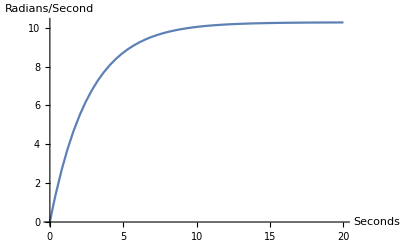

```mathematica
{velUnits, vel} = applyTimeFunction[motorVelocity, aMotorClassic, twelveVoltInput, t];
velUnits // N
Plot[vel, {t, 0, 20}, AxesLabel->{"Seconds", HoldForm[Radians / Second]}, PlotRange->All, AxesOrigin->{0,0}]
```

{2.71828^(-4754.7 t √kg m/(√kg m)) (-3.87693 kg m^2/(s^2 rad))+0.338995 kg m^2/(s^2 rad)+2.71828^(-0.377374 t √kg m/(√kg m)) (3.53793 kg m^2/(s^2 rad))}

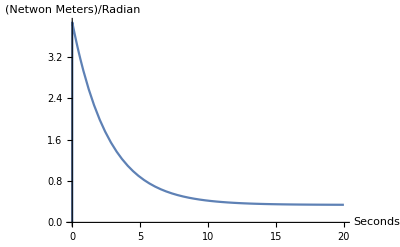

```mathematica
{torUnits, tor} = applyTimeFunction[motorTorque, aMotorClassic, twelveVoltInput, t];
torUnits // N
Plot[tor, {t, 0, 20}, AxesLabel->{"Seconds", HoldForm[Netwon Meters/ Radian]}, PlotRange->All, AxesOrigin->{0,0}]
```

{2.71828^(-4754.7 t √kg m/(√kg m)) (-3.63689 A)+0.318007 A+2.71828^(-0.377374 t √kg m/(√kg m)) (3.31888 A)}

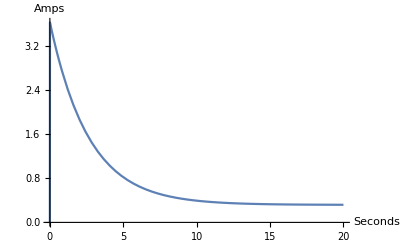

```mathematica
{curUnits, cur} = applyTimeFunction[motorCurrent, aMotorClassic, twelveVoltInput, t];
curUnits // N
Plot[cur, {t, 0, 20}, AxesLabel->{"Seconds", HoldForm[Amps]}, PlotRange->All, AxesOrigin->{0,0}]
```

{2.71828^(-0.377374 t √kg m/(√kg m)) (-10.9514 V)+2.71828^(-4754.7 t √kg m/(√kg m)) (0.000869201 V)+10.9506 V}

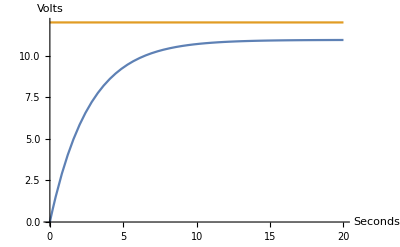

```mathematica
{emfUnits, emf} = applyTimeFunction[motorEMF, aMotorClassic, twelveVoltInput, t];
emfUnits // N // simplifyUnits
Plot[{emf, constvapp /. twelveVoltInput}, {t, 0, 20}, AxesLabel->{"Seconds", HoldForm[Volts]}, PlotRange->All, AxesOrigin->{0,0}]
```

{2.71828^(-4754.7 t √kg m/(√kg m)) (-1.7149×10^-7 rad)+2.71828^(-0.377374 t √kg m/(√kg m)) (27.2234 rad)+4.12469×10^-8 (-6.60011×10^8+2.49051×10^8 t) rad}

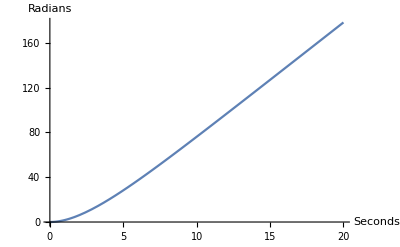

```mathematica
{posUnits, pos} = applyTimeFunction[motorPosition, aMotorClassic, twelveVoltInput, t];
posUnits // N
Plot[pos, {t, 0, 20}, AxesLabel->{"Seconds", HoldForm[Radians]}, PlotRange->All, AxesOrigin->{0,0}]
```

#### Section.Subsection.Subsubsection. Examples with gear, using flywheel load

<|R→3.3,L→0.000694,Ke→0.0177667,Kt→0.0177667,J→0.00001041,B→0.033,Ν→60.,η→0.9,Jafter→0.0096,Bafter→0.,constτappafter→0.|>

<|t→t,constvapp→12.|>

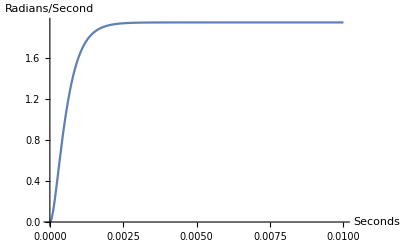

```mathematica
unitlessMotorWithFlywheel  = addMotorLoad[motorParameters["AM 60 A"], flywheel[Quantity[3, "kg"], Quantity[8,"cm"]]] // siUnits // clearUnits // N
twelveVoltInput // siUnits // clearUnits //N
{velUnits2, vel2} = applyTimeFunction[motorVelocity, unitlessMotorWithFlywheel, twelveVoltInput // siUnits // clearUnits // N, t];
Plot[vel2, {t, 0, .01}, AxesLabel->{"Seconds", HoldForm[Radians / Second]}, PlotRange->All, AxesOrigin->{0,0}]
```

#### Section.Subsection.Subsubsection. Examples without gear, using flywheel load

<|R→3.3,L→0.000694,Ke→1.066,Kt→1.066,J→0.00001041,B→0.033,Ν→1.,η→1.,Jafter→0.0096,Bafter→0.,constτappafter→0.|>

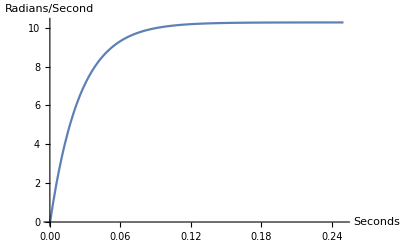

```mathematica
unitlessMotorWithFlywheelNoGear  = addMotorLoad[motorParameters["AM 60 A", Geared-> False], flywheel[Quantity[3, "kg"], Quantity[8,"cm"]]] // siUnits // clearUnits // N
{velUnits3, vel3} = applyTimeFunction[motorVelocity, unitlessMotorWithFlywheelNoGear, twelveVoltInput // siUnits // clearUnits // N, t];
Plot[vel3, {t, 0, 0.25}, AxesLabel->{"Seconds", HoldForm[Radians / Second]}, PlotRange->All, AxesOrigin->{0,0}]
```

## Section. Steady State

### Section.Subsection. Calculating Steady State Values : The Final Value Theorem

We explore the steady state behavior, the limit of the time domain functions as time goes to infinity.

One way to calculate said limit is to brute-force calculate the limit in question. While that works, and we can and have previously calculated same (Ref: https://github.com/rgatkinson/RobotPhysics/blob/master/MotorPhysics.pdf), it is very slow to do so.

A more efficient way to calculate the steady state behavior is to avail ourselves of the use of the Final Value Theorem (Ref: https://en.wikipedia.org/wiki/Final_value_theorem). The final value theorem tells us that if the time-domain limit exists, it is equal to the limit of the Laplace transform of the time domain function as s → 0.

```mathematica
Clear[ssFinalValueTheorem]
ssFinalValueTheorem[model_, inputs_] := Module[{s(*= Unique[]*), t (*= Unique[]*), xformedInputs, expr},
xformedInputs = LaplaceTransform[#[t], t, s] &/@ inputs; 
expr = (model[s] .xformedInputs)[[1]]; 
(*Limit is really slow if we include assumptions (!?), so don't*)
Block[{$Assumptions={}}, Limit[s expr, s -> 0] // FullSimplify]
]
```

```mathematica
(ss = {
ssPos -> ssFinalValueTheorem[motorPositionModel, {constvapp&, constτappafter&}] // Factor,
ssVel -> ssFinalValueTheorem[motorVelocityModel, {constvapp&, constτappafter&}] // Factor,
ssAcc -> ssFinalValueTheorem[motorAccelerationModel, {constvapp&, constτappafter&}] // Factor,
ssEmf -> ssFinalValueTheorem[motorEMFModel, {constvapp&, constτappafter&}] // Factor,
ssCur -> ssFinalValueTheorem[motorCurrentModel, {constvapp&, constτappafter&}] // Factor,
ssTor -> ssFinalValueTheorem[motorTorqueModel, {constvapp&, constτappafter&}] // Factor
}) // prettyPrint
ss /. {Ν -> 1, η-> 1, constτappafter-> 0} // FullSimplify //prettyPrint
```

ssPos→Indeterminate
ssVel→(Ν (constτappafter R+constvapp Kt η Ν))/(Ke Kt η Ν^2+B R η Ν^2+Bafter R)
ssAcc→0
ssEmf→(Ke Ν (constτappafter R+constvapp Kt η Ν))/(Ke Kt η Ν^2+B R η Ν^2+Bafter R)
ssCur→(B constvapp η Ν^2-constτappafter Ke Ν+Bafter constvapp)/(Ke Kt η Ν^2+B R η Ν^2+Bafter R)
ssTor→(Kt (B constvapp η Ν^2-constτappafter Ke Ν+Bafter constvapp))/(Ke Kt η Ν^2+B R η Ν^2+Bafter R)

ssPos→Indeterminate
ssVel→(constvapp Kt)/(Ke Kt+(B+Bafter) R)
ssAcc→0
ssEmf→(constvapp Ke Kt)/(Ke Kt+(B+Bafter) R)
ssCur→((B+Bafter) constvapp)/(Ke Kt+(B+Bafter) R)
ssTor→((B+Bafter) constvapp Kt)/(Ke Kt+(B+Bafter) R)

The “Indeterminate” result regarding position is Mathematica informing us that it has proven to itself that the limit does not exist.

```mathematica
saveDefinitions[outputDirectory <> "SteadyState.m", {ss}]
```

### Section.Subsection. On the Applicability of the Final Value Theorem

Can we always use the Final Value Theorem?

No, the Final Value Theorem only applies under certain conditions. Specifically: that all non-zero poles of the transfer function must have negative real parts, and the transfer function must have at most one pole at the origin (Ref: http://www-personal.umich.edu/~dsbaero/others/39-FVTrevisited.pdf). The predicate exhibited in the ConditionalExpression of the brute-force result captures exactly these conditions. When using the Final Value Theorem on any concrete system, we will need to test the conditions in any particular application. Lets illustrate by looking at the velocity model.

```mathematica
motorVelocityModel 
(velPoles = TransferFunctionPoles[motorVelocityModel]) // MatrixForm
```

(Kt η Ν^2)/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))(Ν (R+L s))/(Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+η Ν^2 (B+J s)))vappτappafterωTransferFunctionModelTrueTrueFalseFalse$Failedvappτappafterω#$CellContext`s21$CellContext`Kt$CellContext`R$CellContext`Ke1111221TrueTrueFalseAutomaticvappτappafterωAutomatic

(((-Bafter L-Jafter R-B L η Ν^2-J R η Ν^2-√(-4 (Jafter L+J L η Ν^2) (Bafter R+Ke Kt η Ν^2+B R η Ν^2)+(Bafter L+Jafter R+B L η Ν^2+J R η Ν^2)^2))/(2 (Jafter L+J L η Ν^2))
(-Bafter L-Jafter R-B L η Ν^2-J R η Ν^2+√(-4 (Jafter L+J L η Ν^2) (Bafter R+Ke Kt η Ν^2+B R η Ν^2)+(Bafter L+Jafter R+B L η Ν^2+J R η Ν^2)^2))/(2 (Jafter L+J L η Ν^2))) | ((-Bafter L-Jafter R-B L η Ν^2-J R η Ν^2-√(-4 (Jafter L+J L η Ν^2) (Bafter R+Ke Kt η Ν^2+B R η Ν^2)+(Bafter L+Jafter R+B L η Ν^2+J R η Ν^2)^2))/(2 (Jafter L+J L η Ν^2))
(-Bafter L-Jafter R-B L η Ν^2-J R η Ν^2+√(-4 (Jafter L+J L η Ν^2) (Bafter R+Ke Kt η Ν^2+B R η Ν^2)+(Bafter L+Jafter R+B L η Ν^2+J R η Ν^2)^2))/(2 (Jafter L+J L η Ν^2))))

The poles are the same for both applied-voltage and applied-torque input since the transfer function denominator is the same for both inputs, in both cases the zeros of:

```mathematica
den = motorVelocityModel[s][[1,1]] // Denominator
```

Ke Kt η Ν^2+(R+L s) (Bafter+Jafter s+(B+J s) η Ν^2)

In order to get a feel for where these zeros are in practice, let’s look at that denominator for an actual example motor. We compute where the poles occur for one of our examples

```mathematica
den /. aMotorClassic /. parameterQuantities // siUnits // clearUnits
Solve[% == 0, s] // N
```

284089/250000+(33/10+(347 s)/500000) (33/1000+(100001041 s)/100000000)

{{s→-0.377374},{s→-4754.7}}

This, for this example, the Final Value Theorem applies. As another example, adding a ridiculous additional load moves the poles, but they remain in the LHS of the complex plane.

```mathematica
den /. addMotorLoad[aMotorClassic, flywheel[Quantity[1000, "kg"], Quantity[1, "m"]]] /. parameterQuantities // siUnits // clearUnits
Solve[% == 0, s] // N
```

284089/250000+(33/10+(347 s)/500000) (33/1000+(50100001041 s)/100000000)

{{s→-0.000753194},{s→-4755.04}}

An analogous analytic development awaits a future revision to this document, as do examples that involve gears or externally applied torque.

## Section. More Administrivia

```mathematica
saveDefinitions[outputDirectory <> "Misc.m", {importMotorData, motorParameters, motorLoad, flywheel, addMotorLoad, massOnPulley, applyTimeFunction}]
```

## Section. Revision History

2018.07.23 Added acceleration-dependant external torque. Corrected “viscous friction” to “viscous drag”. Clarified usage of units.

2018.08.06 Added gearbox support, removed time consuming internal tests. Regularized state variable names. Removed (flawed) “Back EMF vs Applied Voltage” discussion

2018.08.06 Renamed variables. Remove setting $Assumptions (that can slow things down)